# Neutrino Oscillation Potentials

## Brett Deaton Oct 2015

In this formulation, we won't multiply our energy abscissa (p_t) by the redshift. We keep the definition of both the test neutrino and the ambient neutrino potential in terms of the asymptotic energy, p_t. This may be a useful formulation, because along a trajectory defined by fixed p_t, f_ν is constant.

## Initialize Notebook

Read in configuration notebook, and set a bunch of constants.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mbdeaton/code/BrettCodeProjects/NuPotentialsNBs

### Read config file

```mathematica
Get["nu_and_matter_potentials_simulation-config.m"];
```

Now you have:

trajectoryThetadeg			polar angle of the trajectory in deg: e.g. on-axis 0, on-equator 90
trajectoryName				trajectoryThetadeg<>"deg": e.g. on-axis 00deg, on-equator 90deg
runDirectory				where goes the output of this notebook
observationDirectories			where to find the neutrino distribution functions
levName
matterDirectory			where to find the matter profiles

numTopCommentLines
numColumns
numqBins				p_t: energy
numcosABins				cos A: polar angle
numBBins				B: azimuthal angle
qMinMeV
qMaxMeV
cosAMins				a list of (cos A)_min
cosAMaxs				a list of (cos A)_max, usually {1,1,...}
orientPretty
findBestPointing
rTocmDirName			conversion factor to take r to cm

observationDirectories
radiicm
numObservations

numTopCommentLinesFern
numColumnsFern
rMinFerncm
rMaxFerncm
numrBinsFern
rTocmFern				conversion factor to take r to cm

### Set up status file

```mathematica
statusFile=Directory[]<>
"/nu_potentials-"<>
trajectoryName<>
"-"<>
DateString[{"Year","Month","Day","Hour","Minute"}]<>
".out"
```

/Users/mbdeaton/code/BrettCodeProjects/NuPotentialsNBs/nu_potentials-00deg-201601261309.out

Create a simple function for printing to output with no auto linebreaks or superfluous quotation marks.

```mathematica
SetOptions[OpenAppend,PageWidth->∞];
PrintToStatusFile[line_String]:=PutAppend[OutputForm[line],statusFile]
```

```mathematica
PrintToStatusFile["Output file generated on "<>
DateString[]<>
" by\n"<>
ToString[NotebookFileName[]]]
```

### Define constants

#### Fundamental physical constants

From PDG Booklets from 2010-2014.

```mathematica
e=1.602176487*10^-19;(* C, or J/eV *)
mpMeV=938.272013;
mnMeV=939.565346;
muMeV=0.5mpMeV+0.5mnMeV;
cSI=2.99792458*10^8;(* m/s *)
hbarSI=1.054571628*10^-34;(* J s *)
GFNat=1.16637*10^-11;(* this is Subscript[G, F]/(c)^3, with =c=1; units are MeV^-2 *)
```

#### Experimental neutrino parameters

For the following values, a normal ordering is m_1<m_2<m_3 (inverted is m_3<m_1<m_2).

```mathematica
δm21eV2:=7.59*10^-5(* Subscript[m, 2]^2-Subscript[m, 1]^2 *)
δm32eV2:=2.43*10^-3(* |Subscript[m, 3]^2-Subscript[m, 2]^2| *)
θ13:=9./180 π
θ12:=34.4/180 π
θ32:=45./180 π
```

```mathematica
Table[Sin[θ]^2,{θ,{θ13,θ12,θ32}}]
```

{0.0244717,0.319188,0.5}

#### Conversion factors

```mathematica
mTocm:=N[10^2]
kgTog:=N[10^3]
JToerg:=mTocm^2 kgTog
eVToMeV:=N[10^-6]
JToMeV:=1/e*eVToMeV
MeVToerg:=JToerg/JToMeV
MeVc2Tog:=MeVToerg/(cSI*mTocm)^2
```

The naturalized system uses ℏ=c=1, and energy units of MeV.

```mathematica
cmToNat:=(((hbarSI*cSI)/(1/JToMeV))*mTocm)^-1
gToNat:=(MeVToerg/ccgs^2)^-1
```

#### Units in other Systems

```mathematica
ccgs=cSI*mTocm
mug=muMeV*MeVc2Tog
hbarcgs=hbarSI*JToerg(* erg s *)
GFMeVcm=GFNat*(hbarcgs*ccgs)/MeVToerg(* cm/MeV *)
```

2.99792×10^10

1.67377×10^-24

1.05457×10^-27

2.30156×10^-22

## Define Potentials

### Vacuum Potential

V_v_ij(ε)=δm_ij^2/(2ε)

```mathematica
Vv21erg[qMeV_]:=(δm21eV2*eVToMeV^2)/(2qMeV)MeVToerg
Vv32erg[qMeV_]:=(δm32eV2*eVToMeV^2)/(2qMeV)MeVToerg
```

### Matter Potential

V_e=√2 G_F (n_(e^-)-n_(e^+))
V_e=√2 G_F(ϱ Y_e)/m_u

#### Potential at a sample point

```mathematica
Veerg[ϱcgs_,Ye_]:=√2 GFNat((ϱcgs*gToNat/cmToNat^3) Ye)/(mug*gToNat)MeVToerg
```

#### Potential over a list of sample points

Here we  apply the function to some density and electron fraction data:

```mathematica
(* ϱ and v are arrays: e.g. {{Subscript[r, 1],ϱ(Subscript[r, 1])},{Subscript[r, 2],ϱ(Subscript[r, 2])},...}, r in cm *)
VeergList[ϱcgs_,Ye_]:=Block[
(* compose arg array {{Subscript[r, 1],ϱ(Subscript[r, 1]),v(Subscript[r, 1])},{Subscript[r, 2],ϱ(Subscript[r, 2]),v(Subscript[r, 2])},...} for Veerg function *)
{scratch=Join[Transpose[{ϱcgs[[All,2]]}],Transpose[{Ye[[All,2]]}],2]},

Transpose[
Append[
{ϱcgs[[All,1]]},(* r values *)
Map[Veerg@@#&,scratch](* Subscript[V, e] values *)
]]
]
```

### Neutrino Potential

At the same point in space, you find different self-interaction potentials for different test trajectories. So this definition includes two angles to define the trajectory of the test (oscillating) neutrino, (θ, ϕ). The integration angles (A,B), are for the ambient neutrino field.

H_νν has only one non-zero component at t=0 (? Malkus 2015 top of p.5; because V_ν_μ=V_((ν̄)_μ)?), H_νν[ν_e,ν_e]≡V_ν. It is composed of V_ν=V_ν_e-V_((ν̄)_e).

V_ν_e(θ,ϕ)=(√2 G_F)/(8 π^3)∫q^2 ⅆq∫ⅆBⅆ(cosA)(1-cosΘ)f_ν_e(q,A,B)
V_ν_e(θ,ϕ)~(√2 G_F)/(8 π^3)Δq ΔB Δ(cosA)∑ΔV_ν_e[q,A,B]
with ΔV_ν_e[q,A,B]≡q^2(1-cosΘ)f_ν_e[q,A,B]
where the 1/8 π^3 comes from the factor of 1/h^3 in the integral, which in naturalized units is 1/(2π)^3.

The coordinate system over which f_ν is defined has cartesian components P_{x,y,z}. It is rotated with respect to the evolution coordinate system, p_{x,y,z}, so that the P_z-momentum axis aligns with p_r. The spherical polar angles used to define the trajectory in the rotated frame are (A,B). In the rotated frame, the oscillating neutrino's trajectory is (A',B'), and the ambient neutrino's is (A,B).

The angle between the test neutrino's and the ambient neutrino's trajectory, assuming Minkowski spacetime, is very simple in the rotated frame:
cosΘ=cos A' cos A + sin A' sin A cos(B'-B)=cos A

Assumptions about fnue:
- 4D array, with elements fnue[i,j,k,l], where the i,j,k indices correspond to q, cosA, B, and the l index picks one of {q,cosA,f}. (B is not used in this calculation).
- covers a circular patch of sky (all B angles) at zenith given by A∈(cosΑmin,1), and B∈[0,2π). (Although B_{min,max} don't matter in this calculation, only ΔB=2π.)
- spans the asymptotic energies p_t∈(qMinMeV,qMaxMeV].
Note, these bounds are exactly those specified when running the ComputeDistribFunction code (which are not the actual min/max values in the table).
From the bounds we compute Δq, ΔcosA, ΔB.

#### Potential contributed by a single energy bin

```mathematica
Vnuierg::arglengtherr="A different number of samples expected in arg fnu.";
Vnuierg::argdeptherr="A different structure of arg fnu expected.";
```

```mathematica
Vnuierg[fnu_,(* array of data *)
qMinMeV_,qMaxMeV_,(* Subscript[p, t] bounds *)
cosAMin_,cosAMax_(* cosA bounds *)
]:=
Block[
{Nq=numqBins,
NA=numcosABins,
NB=numBBins,
Δq=(qMaxMeV-qMinMeV)/Nq,
ΔcosA=(cosAMax-cosAMin)/NA,
ΔB=(2π)/NB,
returnArray=ConstantArray[{},numqBins]},

If[Depth[fnu]≠5,Message[Vnuierg::argdeptherr];Abort[]];
If[Length[fnu]≠Nq,Message[Vnuierg::arglengtherr];Abort[]];
If[Length[fnu[[1]]]≠NA,Message[Vnuierg::arglengtherr];Abort[]];
If[Length[fnu[[1,1]]]≠NB,Message[Vnuierg::arglengtherr];Abort[]];

For[i=1,i≤Nq,++i,
returnArray[[i]]=Sum[
Block[
{q=fnu[[i,j,k,1]],
CosΘ=fnu[[i,j,k,2]],
f=fnu[[i,j,k,3]]},
q^2(1-CosΘ)f
],
{j,1,NA},
{k,1,NB}
]
];
returnArray*=(√2 GFNat)/(8 π^3)*Δq*ΔcosA*ΔB*MeVToerg
]
```

#### Total potential contributed by neutrinos of all energies

```mathematica
Vnuerg[fnu_,(* array of data *)
qMinMeV_,qMaxMeV_,(* Subscript[p, t] bounds *)
cosAMin_,cosAMax_(* cosA bounds *)
]:=
Block[{scratchArray},
scratchArray=Vnuierg[fnu,
qMinMeV,qMaxMeV,
cosAMin,cosAMax];
Total[scratchArray]
]
```

Alternative lightweight footprint: sum over potentials already computed by Vnuierg.

```mathematica
Vnuerg[Vnuierg_]:=Total[Vnuierg]
```

## Read data

### Import f_ν

The distribution function f(q,cosA,B) is stored in an ascii dat file as (q_i, cosA_j,B_k,f_ijk). The dat file cycles through q, then cos A, then B, with ranges:
q∈[qMinMeV,qMaxMeV] MeV
cosA∈(cosAmin,cosAmax)
B∈[0,2π)

```mathematica
numRowsDistribFunction=numqBins*numcosABins*numBBins;
PrintToStatusFile["We will attempt to read in "<>
ToString[numRowsDistribFunction]<>
" energy+angle bins from each of the "<>
ToString[numObservations]<>
" samples of the nue and nua distribution functions."]
```

The return object of GetDistribFunctionFromDat is a 4D array, but I prefer to think of it as a 3D array of lists having Length==3: {ε_ijk,cosA_ijk,f_ijk}. For example, if we have 20 bins in each dimension, and the returned array, fnu, represents f(p_t,A,B), then
f(qMin MeV, cosAMin, BMin) = fnu[1,1,1,3], or
f(qMax MeV, cosAMin+ΔcosA, BMin) = fnu[20,2,1,3]

```mathematica
GetDistribFunctionFromDat[filename_String]:=Module[
{returnArray},

PrintToStatusFile["Reading "<>filename];

returnArray=Transpose[
Partition[
Partition[
Import[filename,
"Data",
"HeaderLines"->numTopCommentLines,
"IgnoreEmptyLines"->True]
,numqBins]
,numcosABins]
,{3,2,1}];

PrintToStatusFile["comprising "<>
ToString[Length[Flatten[returnArray]]/numColumns]<>" samples."];

returnArray[[All,All,All,{1,2,4}]](* don't return B column *)
]
```

Make a list of filenames pointing to the distribution functions used in this sample.

```mathematica
fnueFilenames=
FileNameJoin[{runDirectory,#,levName,"DistributionFunction-nue.dat"}]&/@observationDirectories;
fnuaFilenames=
FileNameJoin[{runDirectory,#,levName,"DistributionFunction-nua.dat"}]&/@observationDirectories;
```

Read the distribution functions on file into arrays.

```mathematica
fnues=GetDistribFunctionFromDat/@fnueFilenames;
fnuas=GetDistribFunctionFromDat/@fnuaFilenames;
```

```mathematica
PrintToStatusFile[
ToString[MemoryInUse[]/2.^20]<>
" MB in use, "<>
ToString[(ByteCount[fnues]+ByteCount[fnuas])/2.^20]<>
" MB used to store fs."];
```

### Import ϱ and Y_e

From Fernandez, the data x(r) are stored on a grid as (r_i, θ_j,x_ij), and the dat files cycle through r.08, with range r∈3×[10^1,10^4] km, evenly spaced in log r.

```mathematica
numRowsFern=numrBinsFern;
PrintToStatusFile["We will attempt to read in "<>
ToString[numRowsFern]<>
" radial samples from the matter profiles."]
```

The return object of GetMatterProfileFromDat is a 2D array, but I prefer to think of it as a list of lists having Length==2: {r_i,ϱ_i}, or {r_i,Ye_i}. For example, if we have 385 radial bins, and the returned array, ϱFern, represents ϱ(r), then
ϱ(rMinFerncm) = ϱFern[1,2], or
ϱ(rMinFerncm+Δrcm) = ϱFern[2,2]

```mathematica
GetMatterProfileFromDat[filename_String]:=Module[
{returnArray},

SetDirectory[matterDirectory];

PrintToStatusFile["Reading "<>filename];

returnArray=Import[filename,
"Data",
"HeaderLines"->numTopCommentLinesFern,
"IgnoreEmptyLines"->True
];

ResetDirectory[];

PrintToStatusFile["comprising "<>
ToString[Length[Flatten[returnArray]]/numColumnsFern]<>" samples."];

TimesBy[returnArray[[All,1]],rTocmFern];(* scale r to cm *)

returnArray[[All,{1,3}]](* don't return θ column *)
]
```

Make lists of filenames pointing to matter profiles.

```mathematica
ϱFernFilename=FileNameJoin[
{matterDirectory,
"dens_ascii_190-"<>trajectoryName<>".dat"}];
YeFernFilename=FileNameJoin[
{matterDirectory,
"efrc_ascii_190-"<>trajectoryName<>".dat"}];
```

Read matter profiles from file into arrays.

```mathematica
ϱFern=GetMatterProfileFromDat[ϱFernFilename];
YeFern=GetMatterProfileFromDat[YeFernFilename];
```

```mathematica
PrintToStatusFile[
ToString[MemoryInUse[]/2.^20]<>
" MB in use, "<>
ToString[(ByteCount[ϱFern]+ByteCount[YeFern])/2.^20]<>
" MB used to store rho and Ye."];
```

## Calculate Potentials

### Vacuum Potential

For now, just look at an average energy of, I don't know, 10 MeV.

```mathematica
Vv21erg[10]
Vv32erg[10]
```

6.08026×10^-24

1.94664×10^-22

### Matter Potential

```mathematica
VeergFern=VeergList[ϱFern,YeFern];
```

### Neutrino Potential

#### Calculate potentials contributed by each energy bin

In symbol names below "i" indicates that individual energy bins are represented.

```mathematica
VnueiPointserg=Map[Vnuierg[#1,qMinMeV,qMaxMeV,#2,#3]&@@#&,
Transpose[{fnues,cosAMins,cosAMaxs}]];
VnuaiPointserg=Map[Vnuierg[#1,qMinMeV,qMaxMeV,#2,#3]&@@#&,
Transpose[{fnuas,cosAMins,cosAMaxs}]];
VnuiPointserg:=VnueiPointserg-VnuaiPointserg
Transpose[Append[{radiicm},VnuiPointserg]]//Grid
```

3000000 | {1.20459×10^-28,3.28714×10^-19,2.43434×10^-18,-2.18938×10^-18,-1.68172×10^-17,-2.03092×10^-17,-2.99936×10^-17,-3.58808×10^-17,-3.99255×10^-17,-4.18121×10^-17,-4.24503×10^-17,-4.11665×10^-17,-3.84249×10^-17,-3.44626×10^-17,-2.97102×10^-17,-2.46886×10^-17,-1.98516×10^-17,-1.54892×10^-17,-1.17954×10^-17,-8.77951×10^-18}
6000000 | {-1.85834×10^-46,5.59291×10^-20,6.71141×10^-19,-2.36575×10^-19,-3.49581×10^-18,-5.96975×10^-18,-8.15283×10^-18,-8.97155×10^-18,-1.00248×10^-17,-1.06702×10^-17,-1.04556×10^-17,-9.93126×10^-18,-9.16022×10^-18,-8.11203×10^-18,-6.90274×10^-18,-5.64056×10^-18,-4.41635×10^-18,-3.32524×10^-18,-2.41566×10^-18,-1.70464×10^-18}
12000000 | {7.09191×10^-29,1.90991×10^-20,4.37707×10^-20,-4.43535×10^-20,-3.2294×10^-19,-5.6621×10^-19,-1.04331×10^-18,-1.17624×10^-18,-1.24954×10^-18,-1.30395×10^-18,-1.23615×10^-18,-1.12496×10^-18,-9.9596×10^-19,-8.54352×10^-19,-7.01579×10^-19,-5.49523×10^-19,-4.11035×10^-19,-2.94514×10^-19,-2.03371×10^-19,-1.36174×10^-19}
24000000 | {6.19179×10^-29,3.31725×10^-22,8.48877×10^-21,-2.98898×10^-22,-1.76771×10^-20,-5.16465×10^-20,-7.81735×10^-20,-9.57922×10^-20,-9.91597×10^-20,-9.63285×10^-20,-8.97968×10^-20,-8.08531×10^-20,-6.98872×10^-20,-5.79707×10^-20,-4.59919×10^-20,-3.48268×10^-20,-2.51249×10^-20,-1.73585×10^-20,-1.15584×10^-20,-7.46521×10^-21}
48000000 | {-4.42411×10^-43,1.2263×10^-22,4.84152×10^-22,1.0068×10^-22,-1.31844×10^-21,-3.45751×10^-21,-5.37727×10^-21,-6.46489×10^-21,-6.64945×10^-21,-6.31963×10^-21,-5.79634×10^-21,-5.14907×10^-21,-4.382×10^-21,-3.55728×10^-21,-2.75763×10^-21,-2.03438×10^-21,-1.43072×10^-21,-9.63018×10^-22,-6.24611×10^-22,-3.92822×10^-22}
96000000 | {0.,8.08883×10^-24,2.07561×10^-23,-1.29862×10^-23,-9.64271×10^-23,-2.36988×10^-22,-3.47582×10^-22,-4.14184×10^-22,-4.20454×10^-22,-3.9831×10^-22,-3.63604×10^-22,-3.19397×10^-22,-2.69315×10^-22,-2.16361×10^-22,-1.65676×10^-22,-1.20667×10^-22,-8.38117×10^-23,-5.57162×10^-23,-3.57091×10^-23,-2.22054×10^-23}

#### Debug: look at the structure of this array

```mathematica
VnuiPointserg//TableForm
Transpose[VnuiPointserg]//TableForm
```

1.20459×10^-28 | 3.28714×10^-19 | 2.43434×10^-18 | -2.18938×10^-18 | -1.68172×10^-17 | -2.03092×10^-17 | -2.99936×10^-17 | -3.58808×10^-17 | -3.99255×10^-17 | -4.18121×10^-17 | -4.24503×10^-17 | -4.11665×10^-17 | -3.84249×10^-17 | -3.44626×10^-17 | -2.97102×10^-17 | -2.46886×10^-17 | -1.98516×10^-17 | -1.54892×10^-17 | -1.17954×10^-17 | -8.77951×10^-18
-1.85834×10^-46 | 5.59291×10^-20 | 6.71141×10^-19 | -2.36575×10^-19 | -3.49581×10^-18 | -5.96975×10^-18 | -8.15283×10^-18 | -8.97155×10^-18 | -1.00248×10^-17 | -1.06702×10^-17 | -1.04556×10^-17 | -9.93126×10^-18 | -9.16022×10^-18 | -8.11203×10^-18 | -6.90274×10^-18 | -5.64056×10^-18 | -4.41635×10^-18 | -3.32524×10^-18 | -2.41566×10^-18 | -1.70464×10^-18
7.09191×10^-29 | 1.90991×10^-20 | 4.37707×10^-20 | -4.43535×10^-20 | -3.2294×10^-19 | -5.6621×10^-19 | -1.04331×10^-18 | -1.17624×10^-18 | -1.24954×10^-18 | -1.30395×10^-18 | -1.23615×10^-18 | -1.12496×10^-18 | -9.9596×10^-19 | -8.54352×10^-19 | -7.01579×10^-19 | -5.49523×10^-19 | -4.11035×10^-19 | -2.94514×10^-19 | -2.03371×10^-19 | -1.36174×10^-19
6.19179×10^-29 | 3.31725×10^-22 | 8.48877×10^-21 | -2.98898×10^-22 | -1.76771×10^-20 | -5.16465×10^-20 | -7.81735×10^-20 | -9.57922×10^-20 | -9.91597×10^-20 | -9.63285×10^-20 | -8.97968×10^-20 | -8.08531×10^-20 | -6.98872×10^-20 | -5.79707×10^-20 | -4.59919×10^-20 | -3.48268×10^-20 | -2.51249×10^-20 | -1.73585×10^-20 | -1.15584×10^-20 | -7.46521×10^-21
-4.42411×10^-43 | 1.2263×10^-22 | 4.84152×10^-22 | 1.0068×10^-22 | -1.31844×10^-21 | -3.45751×10^-21 | -5.37727×10^-21 | -6.46489×10^-21 | -6.64945×10^-21 | -6.31963×10^-21 | -5.79634×10^-21 | -5.14907×10^-21 | -4.382×10^-21 | -3.55728×10^-21 | -2.75763×10^-21 | -2.03438×10^-21 | -1.43072×10^-21 | -9.63018×10^-22 | -6.24611×10^-22 | -3.92822×10^-22
0. | 8.08883×10^-24 | 2.07561×10^-23 | -1.29862×10^-23 | -9.64271×10^-23 | -2.36988×10^-22 | -3.47582×10^-22 | -4.14184×10^-22 | -4.20454×10^-22 | -3.9831×10^-22 | -3.63604×10^-22 | -3.19397×10^-22 | -2.69315×10^-22 | -2.16361×10^-22 | -1.65676×10^-22 | -1.20667×10^-22 | -8.38117×10^-23 | -5.57162×10^-23 | -3.57091×10^-23 | -2.22054×10^-23

1.20459×10^-28 | -1.85834×10^-46 | 7.09191×10^-29 | 6.19179×10^-29 | -4.42411×10^-43 | 0.
3.28714×10^-19 | 5.59291×10^-20 | 1.90991×10^-20 | 3.31725×10^-22 | 1.2263×10^-22 | 8.08883×10^-24
2.43434×10^-18 | 6.71141×10^-19 | 4.37707×10^-20 | 8.48877×10^-21 | 4.84152×10^-22 | 2.07561×10^-23
-2.18938×10^-18 | -2.36575×10^-19 | -4.43535×10^-20 | -2.98898×10^-22 | 1.0068×10^-22 | -1.29862×10^-23
-1.68172×10^-17 | -3.49581×10^-18 | -3.2294×10^-19 | -1.76771×10^-20 | -1.31844×10^-21 | -9.64271×10^-23
-2.03092×10^-17 | -5.96975×10^-18 | -5.6621×10^-19 | -5.16465×10^-20 | -3.45751×10^-21 | -2.36988×10^-22
-2.99936×10^-17 | -8.15283×10^-18 | -1.04331×10^-18 | -7.81735×10^-20 | -5.37727×10^-21 | -3.47582×10^-22
-3.58808×10^-17 | -8.97155×10^-18 | -1.17624×10^-18 | -9.57922×10^-20 | -6.46489×10^-21 | -4.14184×10^-22
-3.99255×10^-17 | -1.00248×10^-17 | -1.24954×10^-18 | -9.91597×10^-20 | -6.64945×10^-21 | -4.20454×10^-22
-4.18121×10^-17 | -1.06702×10^-17 | -1.30395×10^-18 | -9.63285×10^-20 | -6.31963×10^-21 | -3.9831×10^-22
-4.24503×10^-17 | -1.04556×10^-17 | -1.23615×10^-18 | -8.97968×10^-20 | -5.79634×10^-21 | -3.63604×10^-22
-4.11665×10^-17 | -9.93126×10^-18 | -1.12496×10^-18 | -8.08531×10^-20 | -5.14907×10^-21 | -3.19397×10^-22
-3.84249×10^-17 | -9.16022×10^-18 | -9.9596×10^-19 | -6.98872×10^-20 | -4.382×10^-21 | -2.69315×10^-22
-3.44626×10^-17 | -8.11203×10^-18 | -8.54352×10^-19 | -5.79707×10^-20 | -3.55728×10^-21 | -2.16361×10^-22
-2.97102×10^-17 | -6.90274×10^-18 | -7.01579×10^-19 | -4.59919×10^-20 | -2.75763×10^-21 | -1.65676×10^-22
-2.46886×10^-17 | -5.64056×10^-18 | -5.49523×10^-19 | -3.48268×10^-20 | -2.03438×10^-21 | -1.20667×10^-22
-1.98516×10^-17 | -4.41635×10^-18 | -4.11035×10^-19 | -2.51249×10^-20 | -1.43072×10^-21 | -8.38117×10^-23
-1.54892×10^-17 | -3.32524×10^-18 | -2.94514×10^-19 | -1.73585×10^-20 | -9.63018×10^-22 | -5.57162×10^-23
-1.17954×10^-17 | -2.41566×10^-18 | -2.03371×10^-19 | -1.15584×10^-20 | -6.24611×10^-22 | -3.57091×10^-23
-8.77951×10^-18 | -1.70464×10^-18 | -1.36174×10^-19 | -7.46521×10^-21 | -3.92822×10^-22 | -2.22054×10^-23

#### Calculate potentials contributed by the sum of all energy bins:

```mathematica
VnuePointserg=Vnuerg/@VnueiPointserg
VnuaPointserg=Vnuerg/@VnuaiPointserg
VnuPointserg:=VnuePointserg-VnuaPointserg
Transpose[Append[{radiicm},VnuPointserg]]//Grid
```

{7.87965×10^-17,2.34512×10^-17,3.44643×10^-18,2.95121×10^-19,1.99789×10^-20,1.28353×10^-21}

{5.2978×10^-16,1.3231×10^-16,1.55977×10^-17,1.16621×10^-18,7.59465×10^-20,4.83408×10^-21}

3000000 | -4.50984×10^-16
6000000 | -1.08859×10^-16
12000000 | -1.21513×10^-17
24000000 | -8.71089×10^-19
48000000 | -5.59676×10^-20
96000000 | -3.55055×10^-21

#### Debug: print a warning if this trajectory doesn't generate the right sign of V_νν to go through an MNR

```mathematica
MapIndexed[
If[Sign[#1]>-1,
PrintToStatusFile["Warning: Vnue>Vnua at r="<>
ToString[radiicm[[First[#2]]]]<>
" cm, so that Vnu="<>
ToString[#1]<>
" erg."]]&,
VnuPointserg];
```

## Make Plots

### Make ListPlot-able arrays

Append radii to V_νν arrays for ListPlots.

```mathematica
VnuiPointsergForPlot:=Table[
MapThread[{#1,#2}&,{radiicm,Transpose[VnuiPointserg][[i]]}],
{i,numqBins}]
VnuPointsergForPlot:=Transpose[Append[{radiicm},VnuPointserg]]
VnuePointsergForPlot:=Transpose[Append[{radiicm},VnuePointserg]]
VnuaPointsergForPlot:=Transpose[Append[{radiicm},VnuaPointserg]]
```

#### Debug: compare V_νν(q) in original and ListPlot-able form

```mathematica
Length[VnuiPointserg]
Length[VnuiPointsergForPlot[[1]]]
```

6

6

```mathematica
Length[VnuiPointserg[[1]]]
Length[VnuiPointsergForPlot]
```

20

20

```mathematica
VnuiPointserg[[All,1]]//TableForm
VnuiPointsergForPlot[[1]]//TableForm
```

1.20459×10^-28
-1.85834×10^-46
7.09191×10^-29
6.19179×10^-29
-4.42411×10^-43
0.

3000000 | 1.20459×10^-28
6000000 | -1.85834×10^-46
12000000 | 7.09191×10^-29
24000000 | 6.19179×10^-29
48000000 | -4.42411×10^-43
96000000 | 0.

### Setup standard plot options

```mathematica
Needs["PlotLegends`"]
```

#### Bounds

Enforce integer powers of 10 for log plots.

```mathematica
rMinPlotcm=10.^Floor[Log[10,VnuiPointsergForPlot[[1,1,1]]]]
rMaxPlotcm=3.*10^Ceiling[Log[10,
Max[
radiicm[[-1]],
10^8]
]](* ≥3000 km *)
```

1.×10^6

3.×10^8

```mathematica
VMinPloterg=10.^Floor[Log[10,
Vv21erg[10]
]](* Subscript[V, vac,21](10MeV) *)
VMaxPloterg=10.^Ceiling[Log[10,
Max[
1.1*Max[Abs/@VnuPointserg],
10^-15]
]](* ≤10^-15 *)
```

1.×10^-24

1.×10^-15

#### Tick Marks

Define a function that will make a list of ≲5 tick marks at multiples of 10^n.

```mathematica
Log10Ticks[min_,max_]:=
Block[
{thisTick=10^Ceiling[Log[10,min]],
Log10TickStep=Max[1,Ceiling[(Log[10,max]-Log[10,min])/5]],
ticks={}},
While[thisTick≤max,
AppendTo[ticks,{thisTick,Superscript[10,Log[10,thisTick]]}];
thisTick*=10^Log10TickStep;
];
ticks]
```

#### Options

```mathematica
brettsPlotOptions={
PlotRange->{{rMinPlotcm,rMaxPlotcm},{VMinPloterg,VMaxPloterg}},
AxesLabel->{"r (cm)","V (erg)"},
Ticks->Log10Ticks,
Joined->True,
ImageSize->Large,
LabelStyle->Directive[FontWeight->"Light",FontSize->14,FontFamily->"Helvetica"]
};
```

```mathematica
brettsLegendOptions={
LegendTextSpace->10,
LegendSize->0.5,
ShadowBackground->Opacity[0],
LegendBackground->Opacity[0],
LegendBorder->None
};
```

```mathematica
brettsLabelOptions={
LabelStyle->Directive[FontWeight->"SemiBold",18,FontFamily->"Helvetica"]
};
```

#### Stylings for Datasets

```mathematica
VnuiStyles=Table[RGBColor[i/19,1-i/19,1-i/19],{i,1,19}];
VnueStyle=Directive[Darker[Red],PointSize[Small]];
VnuaStyle=Directive[Darker[Cyan],PointSize[Small]];
VnuStyle=Directive[Darker[Yellow],PointSize[Medium]];

ϱStyle=Directive[Lighter[Orange],PointSize[Small]];
YeStyle=Directive[Lighter[Blue],PointSize[Small]];
VeStyle=Directive[Blend[{Lighter[Orange],Lighter[Blue]},0.5],PointSize[Medium]];
```

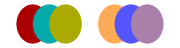

```mathematica
Graphics[
{
VnueStyle,Disk[{0,0}],
VnuaStyle,Disk[{1,0}],
VnuStyle,Disk[{2,0}],
ϱStyle,Disk[{5,0}],
YeStyle,Disk[{6,0}],
VeStyle,Disk[{7,0}]
},
ImageSize->Small]
```

### Plot: V_(νν,q_i)

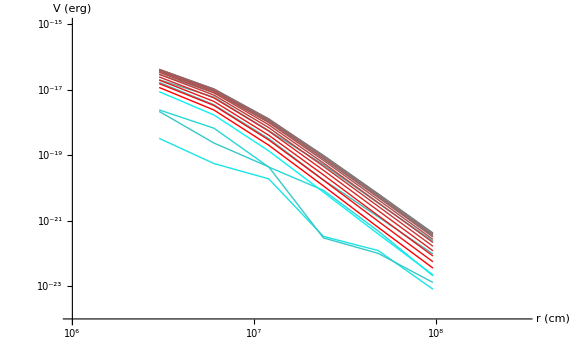
-Graphics-ν self-interaction potentials by different energies (θ=0deg)

potentials-Vnunu_separate_energies-00deg.pdf

```mathematica
plotVnui=ListLogLogPlot[
{
Abs/@VnuiPointsergForPlot
},
PlotStyle->VnuiStyles,
brettsPlotOptions
];
Labeled[
Show[plotVnui],
"ν self-interaction potentials by different energies (θ="<>
ToString[trajectoryThetadeg]<>"deg)",
Top,
brettsLabelOptions
]
Export["potentials-Vnunu_separate_energies-"<>trajectoryName<>".pdf",%]
```

### Plot: V_ν_e with V_((ν̄)_e)

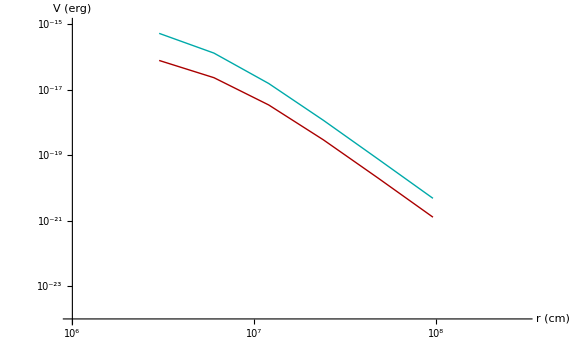
-Graphics-ν self-interaction potentials (θ=0deg)

```mathematica
plotVnueAndVnua=ListLogLogPlot[
{
VnuePointsergForPlot,
VnuaPointsergForPlot
},
PlotStyle->{VnueStyle,VnuaStyle},
brettsPlotOptions,
PlotLegend->{"V_ν_e","V_((ν̄)_e)"},
LegendPosition->{-0.7,-0.45},
brettsLegendOptions
];
Labeled[
Show[plotVnueAndVnua],
"ν self-interaction potentials (θ="<>ToString[trajectoryThetadeg]<>"deg)",
Top,
brettsLabelOptions
]
```

### Plot: V_νν

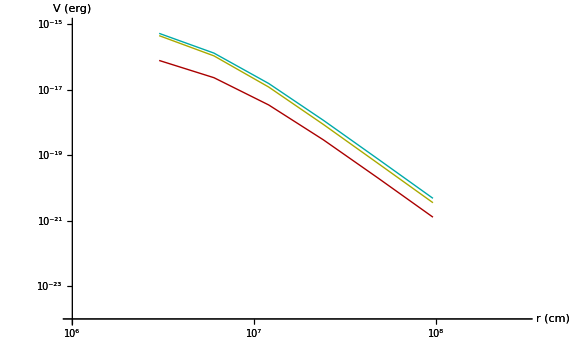
-Graphics-Total ν self-interaction potential (θ=0deg)

potentials-Vnue_Vnua_Vnunu-00deg.pdf

```mathematica
plotVnu=ListLogLogPlot[
{
Abs/@VnuPointsergForPlot
},
brettsPlotOptions,
PlotStyle->VnuStyle,
PlotLegend->{"|V_ν_e-V_((ν̄)_e)|"},
LegendPosition->{-0.7,-0.35},
brettsLegendOptions
];
Labeled[
Show[plotVnu,plotVnueAndVnua],
"Total ν self-interaction potential (θ="<>ToString[trajectoryThetadeg]<>"deg)",
Top,
brettsLabelOptions
]
Export["potentials-Vnue_Vnua_Vnunu-"<>trajectoryName<>".pdf",%]
```

### Plot: V_e

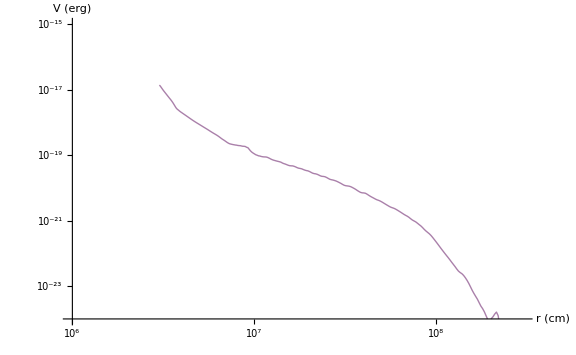
-Graphics-Matter potential (θ=0deg)

```mathematica
plotVe=ListLogLogPlot[
{
VeergFern
},
brettsPlotOptions,
PlotStyle->VeStyle,
PlotLegend->{"V_e"},
LegendPosition->{-0.7,-0.4},
brettsLegendOptions
];
Labeled[
Show[plotVe],
"Matter potential (θ="<>ToString[trajectoryThetadeg]<>"deg)",
Top,
brettsLabelOptions
]
```

### Plot: V_e with V_νν

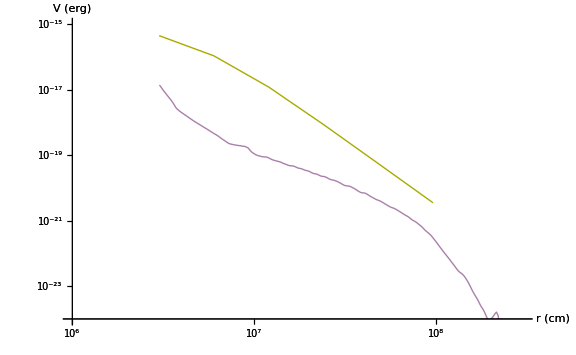
-Graphics-Neutrino Potentials (θ=0deg)

potentials-Ve_Vnunu-00deg.pdf

```mathematica
Labeled[
Show[plotVe,plotVnu],
"Neutrino Potentials (θ="<>ToString[trajectoryThetadeg]<>"deg)",
Top,
brettsLabelOptions
]
Export["potentials-Ve_Vnunu-"<>trajectoryName<>".pdf",%]
```

## ToDos

### Here is a list of ToDos for this notebook

Make it executable from the command line. You cannot just call MathKernel -run "<<nu_potentials.nb", notebooks don't execute that way.

Typeset the degree symbol for the plotlabels. In Mathematica front end, you can get a ◦ superscript with the special character [InvisibleSpace] (preceded by a "\"). But this exports in an ugly mess to pdf.